```mathematica
I
```

ⅈ

```mathematica
i
```

i

```mathematica
i^2
```

i^2

```mathematica
%//Simplify
```

i^2

pure function

```mathematica
#^3 &[x]
```

x^3

```mathematica
Sin (Pi)
```

π Sin

```mathematica
f[x_]:=Sin[x]
```

```mathematica
Sin[#] &[Pi]
```

0

```mathematica
Pi(Sin)
```

π Sin

```mathematica
π[x_]:=x^3
```

SetDelayed::write: Tag π in π[x_] is Protected.

$Failed

```mathematica
FullForm[+]
```

```mathematica
A+2//FullForm
```

Plus[2,A]

# Afternoon

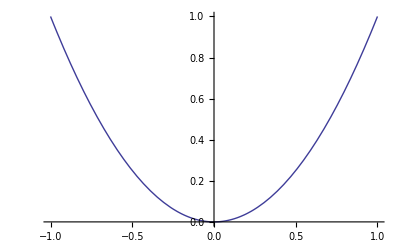

```mathematica
x=5;Plot[x^2,{x,-1,1}]
```

```mathematica
?x
```

Global`x

x=5

```mathematica
??x
```

Global`x

x=5

```mathematica
evaluation
```

```mathematica
Hold[2+2]
```

Hold[2+2]

```mathematica
FullForm[Hold[1+2]]
```

Hold[Plus[1,2]]

```mathematica
FullForm[Hold[a-b]]
```

Hold[Plus[a,Times[-1,b]]]

```mathematica
FullForm[Hold[3-5]]
```

Hold[Plus[3,-5]]

```mathematica
??Minus
```

-x is the arithmetic negation of x.

Attributes[Minus]={Listable,NumericFunction,Protected}

```mathematica
??MinusPlus
```

MinusPlus[x] displays as ∓x.
MinusPlus[x,y,…] displays as x∓y∓….

```mathematica
Clear["Global'*"];
```

```mathematica
Clear[c];??c
```

Global`c

```mathematica
??ClearAll
```

ClearAll[symb_1,symb_2,…] clears all values, definitions, attributes, messages and defaults associated with symbols. 
ClearAll[form,form,…] clears all symbols whose names textually match any of the form_i.

Attributes[ClearAll]={HoldAll,Protected}

```mathematica
ClearAll["Global`*"]
```

```mathematica
{a,b,c}
```

{a,b,c}

```mathematica
v={a,b,c};
w={d,e,f};
```

```mathematica
v . w
```

a d+b e+c f

a d+b e+c f

```mathematica
t=
```

```mathematica
matrix 2D input
```

```mathematica
FullForm[Hold[x=5]]
```

Hold[Set[x,5]]

```mathematica
RandomReal[]
```

0.206177

```mathematica
Histogram[RandomReal[{0,1},1000],20]
```

-Graphics-

```mathematica
Histogram[0.5367470202776767]
```

```mathematica
x^2 Sin[x]/.{x->5}//Hold//FullForm
```

Hold[ReplaceAll[Times[Power[x,2],Sin[x]],List[Rule[x,5]]]]

```mathematica
x^2/.{x->0, x->2}
```

0

```mathematica
Clear[x]
```

```mathematica
x^2+x//FullForm
```

Plus[x,Power[x,2]]

```mathematica
x(x^2+x)//FullForm
```

Times[x,Plus[x,Power[x,2]]]

```mathematica
x(x^2+x)/.{Times -> Hahahah, x-> 1, x^2-> 5}
```

Hahahah[1,6]

```mathematica
Do[RandomReal[{0,1}, 10^6]/.List->Plus, {1000}]//Timing
```

$Aborted

```mathematica
??OwnValues
```

OwnValues[x] gives the rule corresponding to any ownvalue defined for the symbol x.

Attributes[OwnValues]={HoldAll,Protected}
 
Options[OwnValues]={Sort→True}

```mathematica
??Block
```

Block[{x,y,…},expr] specifies that expr is to be evaluated with local values for the symbols x, y, … . 
Block[{x=x_0,…},expr] defines initial local values for x, … .

Attributes[Block]={HoldAll,Protected}

```mathematica
x=5
```

5

```mathematica
x/.x-> 16
```

16

```mathematica
?? /.
```

expr/.rules applies a rule or list of rules in an attempt to transform each subpart of an expression expr.

Attributes[ReplaceAll]={Protected}

```mathematica
x /. {{x->1},{x->2},{x->3}}
```

{1,2,3}

```mathematica
x^2+2x+7==0
```

7+2 x+x^2==0

```mathematica
x^2+2x+7==0//FullForm
```

Equal[Plus[7,Times[2,x],Power[x,2]],0]

```mathematica
Solve[x^2+2x+7==0, x]
```

{{x→-1-ⅈ √6},{x→-1+ⅈ √6}}

```mathematica
Equal[x^2+x,x+7]
```

x+x^2==7+x

```mathematica
Sin[x]^2+Cos[x]^2==1
```

Cos[x]^2+Sin[x]^2==1

```mathematica
Sin[x]^2+Cos[x]^2==1/.x->300
```

True

```mathematica
??===
```

RowBox[{StyleBox["lhs", "TI"], "===", StyleBox["rhs", "TI"]}] yields True if the expression StyleBox["lhs", "TI"] is identical to StyleBox["rhs", "TI"], and yields False otherwise.

Attributes[SameQ]={Protected}

```mathematica
Sin[x]^2+Cos[x]^2===1/.x->300
```

False

```mathematica
x^2== 4
```

```mathematica
x^2==4//Solve
```

{{x→-2},{x→2}}

```mathematica
x/.Solve[x^2==4]
```

{-2,2}

```mathematica
Solve[x^2==2,{x}]//
```

ReplaceAll::reps: {#1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

(x/.#1)[{{x→-√2},{x→√2}}]

```mathematica
#+# &[x]
```

2 x

```mathematica
??//
```

Postfix[f[expr]] prints with f[expr] given in default postfix form: expr//f. 
Postfix[f[expr],h] prints as exprh.

Attributes[Postfix]={Protected}

```mathematica
2// # &
```

2

```mathematica
Solve[x^2==2,{x}]//x /. # &
```

{-√2,√2}

```mathematica
f[x_]:=x^2;
g[t_]:=t^2;
```

```mathematica
f[x]==g[x]
```

True

```mathematica
??DownValues
```

DownValues[f] gives a list of transformation rules corresponding to all downvalues defined for the symbol f.

Attributes[DownValues]={HoldAll,Protected}
 
Options[DownValues]={Sort→True}

```mathematica
DownValues[f]
```

{HoldPattern[f[x_]]:>x^2}

```mathematica
Clear[f]
```

```mathematica
f[x_,y_]:=x^2-y^2
```

```mathematica
Plot3D[f[x,y],{x,-1,1},{-1,1}]
```

```mathematica
pp[ooo_]=ooo^2
```

ooo^2

```mathematica
pp[3]
```

9

```mathematica
??Function
```

Function[body] or body& is a pure function. The formal parameters are # (or #1), #2, etc. 
Function[x,body] is a pure function with a single formal parameter x. 
Function[{x_1,x_2,…},body] is a pure function with a list of formal parameters.

Attributes[Function]={HoldAll,Protected}

```mathematica
Function[x, x^2+1] [π]
```

1+π^2

```mathematica
Solve[x^2==2,{x}]//x/.# &
```

{-√2,√2}

```mathematica
Solve[x^2==2,{x}]//x/.# & [[1,2]]
```

#1[{{x→-√2},{x→√2}}]

```mathematica
Function[{x,y},x^2-y^2+a^2][2,3]
```

-5+a^2

```mathematica
Function[#2^2-#1^2+a^2][2,3]
```

5+a^2

```mathematica
#2^2-#1^2+a^2&[2,3]
```

5+a^2

```mathematica
Solve[x^2==2,{x}]//x/.# &
```

{-√2,√2}

```mathematica
Solve[x^2==2,{x}]//x/.# &
```

{-√2,√2}

```mathematica
lst=RandomInteger[{1,100}, {50}]
```

{79,2,26,89,34,68,78,81,50,21,82,93,75,16,44,13,75,2,15,70,51,33,12,33,24,42,66,60,22,59,95,24,97,29,12,84,64,6,47,95,91,69,28,26,26,22,36,16,56,64}

```mathematica
??Select
```

Select[list,crit] picks out all elements e_i of list for which crit[e_i] is True. 
Select[list,crit,n] picks out the first n elements for which crit[e_i] is True.

Attributes[Select]={Protected}

```mathematica
Select[lst, # > 50 &]
```

{79,89,68,78,81,82,93,75,75,70,51,66,60,59,95,97,84,64,95,91,69,56,64}

```mathematica
Select[lst, EvenQ[#] &]
```

{2,26,34,68,78,50,82,16,44,2,70,12,24,42,66,60,22,24,12,84,64,6,28,26,26,22,36,16,56,64}

```mathematica
??EvenQ
```

RowBox[{"EvenQ", "[", StyleBox["expr", "TI"], "]"}] gives True if StyleBox["expr", "TI"] is an even integer, and False otherwise.

Attributes[EvenQ]={Listable,Protected}

```mathematica
??Split
```

RowBox[{"Split", "[", StyleBox["list", "TI"], "]"}] splits StyleBox["list", "TI"] into sublists consisting of runs of identical elements. 
RowBox[{"Split", "[", RowBox[{StyleBox["list", "TI"], ",", StyleBox["test", "TI"]}], "]"}] treats pairs of adjacent elements as identical whenever applying the function StyleBox["test", "TI"] to them yields True.

Attributes[Split]={Protected}

```mathematica
lst=RandomInteger[{1,100}, {10^6}];
```

```mathematica
incr=Split[lst, #1≤ #2 &];
```

```mathematica
Length[incr]
```

495305

```mathematica
Length[Select[incr,Length[#]≥ 7&]]
```

196

```mathematica
??Map
```

Map[f,expr] or f/@expr applies f to each element on the first level in expr. 
Map[f,expr,levelspec] applies f to parts of expr specified by levelspec.

Attributes[Map]={Protected}
 
Options[Map]={Heads→False}

```mathematica
Length /@ incr // Max
```

10

```mathematica
Select[incr, Length[#]==10 &]
```

{{11,19,22,57,58,65,70,74,75,91}}

```mathematica
??With
```

With[{x=x_0,y=y_0,…},expr] specifies that in expr occurrences of the symbols x, y, … should be replaced by x_0, y_0, … .

Attributes[With]={HoldAll,Protected}

```mathematica
lst=RandomInteger[{1,100}, {10^6}];
incr=Split[lst, #1≤ #2 &];
Length /@ incr // Max
```